# Homework 13

## Part A

Consider a driven damped harmonic oscillator. Using the equation for the amplitude A of the steady-state solution derived in class or the text (Eq. 5.64), plot A as a function of the driving frequency omega.

```mathematica
Quit[]
```

0.1 √(1/(16 omega^2+(1200.-omega^2)^2))

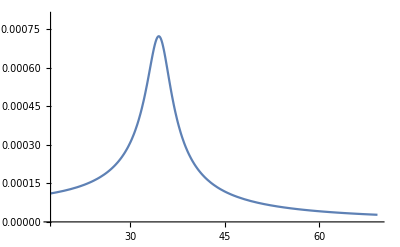

```mathematica
beta=2;
m=.005;
k=6;
f0=.0005/m;
omega0=Sqrt[k/m];
A=Sqrt[f0^2/((omega0^2-omega^2)^2+4*beta^2*omega^2)]
Plot[A,{omega,omega0/2,2omega0},PlotRange->{0,.0008}]
```

## Part B

Now plot  A^2 as a function of the driving frequency. Estimate the maximum and the FWHM of this curve graphically by adjusting the plot range appropriately.Compare this number with 2*beta. Determine the quality factor, Q, of the oscillator.

0.01/(16 omega^2+(1200.-omega^2)^2)

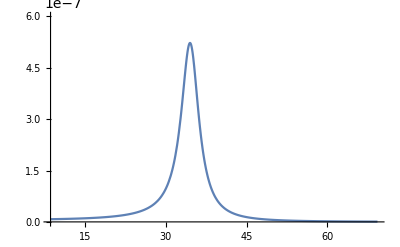

```mathematica
Asq=f0^2/((omega0^2-omega^2)^2+4*beta^2*omega^2)
Plot[Asq,{omega,omega0/4,2*omega0},PlotRange->{0,6*10^(-7)}]
```

Estimate the maximum value of A^2 from the graph above (adjust the PlotRange argument to get a better look if necessary).

```mathematica
A0sq=5.3*10^-7
```

5.3×10^-7

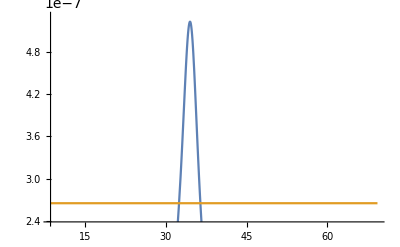

```mathematica
Plot[{Asq,A0sq/2},{omega,omega0/4,2*omega0},PlotRange->{0.9*A0sq/2,A0sq}]
```

```mathematica
2*beta
```

4

```mathematica
FWHM=2*beta;
twobeta=2*beta//N
Q=N[omega0/(2*beta)]
```

4.

8.66025

### Solution

```mathematica
Q$=8.660254040;
If[Abs[Q-Q$]/Q$<.01,Print["Q is correct"],Print["Q is not correct"]]
```

Q is correct

## No written problems for this assignment.